```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

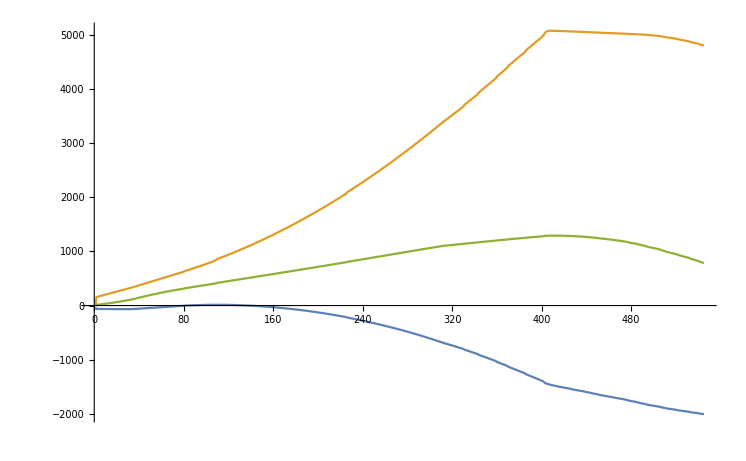

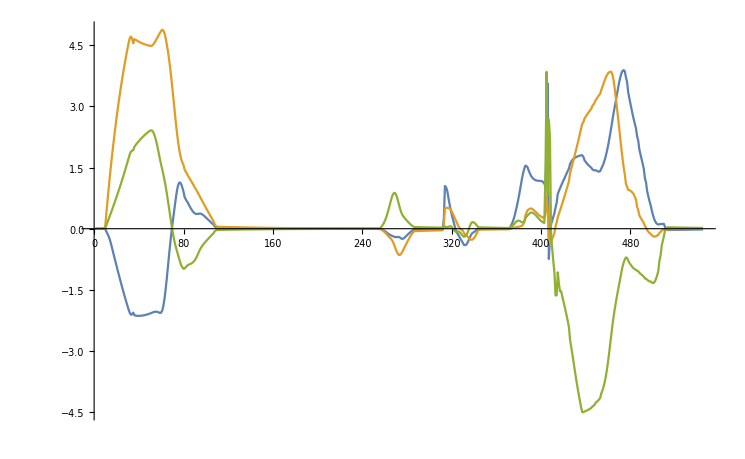

```mathematica
car = #["car"] &  /@ ImportNDJSON["info.ndjson",{2}];
ListLinePlot[Transpose[#["x"]& /@ car], PlotRange->All]
ListLinePlot[Transpose[#["w"]& /@ car], PlotRange->All]
```

```mathematica
{#["on_ground"], #["x"][[3]], #["w"], #["pitch"], #["yaw"], #["roll"]}& /@ car
```

{{True,24.9239,{0.,0.,0.00235336},0.,0.,0.},{True,16.4329,{-0.0034059,-0.000160022,0.0021386},0.,0.,0.},{True,16.4124,{0.00107439,0.,0.00183859},-0.539063,1.,-1.},{True,17.0294,{-0.000049991,0.,0.00156239},-0.289063,1.,-1.},{True,19.5966,{-0.000257617,0.,0.00136238},-0.125,1.,-1.},{True,22.1962,{-0.000457623,0.,0.00118619},-0.492188,1.,-1.},{True,24.8335,{-0.000657629,0.,0.00108619},-0.476563,1.,-1.},{True,27.5007,{-0.000857635,0.,0.000986182},-0.46875,1.,-1.},{False,30.2003,{-0.00101,0.,0.00091},-0.453125,1.,-1.},{False,32.9423,{-0.0145657,0.0759047,0.0182537},-0.445313,1.,-1.},{False,35.7367,{-0.0710386,0.391496,0.0910797},-0.476563,1.,-1.},{False,38.5887,{-0.126688,0.694475,0.16403},-0.640625,1.,-1.},{False,41.4931,{-0.188023,0.985128,0.237227},-0.796875,1.,-1.},{False,44.4575,{-0.265739,1.2635,0.310896},-0.960938,1.,-1.},{False,47.4795,{-0.359742,1.53004,0.385385},-1.,1.,-1.},{False,50.5539,{-0.467727,1.7852,0.461049},-1.,1.,-1.},{False,53.6859,{-0.578364,2.0298,0.537766},-1.,1.,-1.},{False,56.8703,{-0.6883,2.26439,0.615407},-1.,1.,-1.},{False,60.1147,{-0.797489,2.48938,0.694048},-1.,1.,-1.},{False,63.4167,{-0.905754,2.70517,0.773737},-1.,1.,-1.},{False,66.7712,{-1.01299,2.91212,0.854626},-1.,1.,-1.},{False,70.1832,{-1.11909,3.11059,0.936738},-1.,1.,-1.},{False,73.6452,{-1.22386,3.30104,1.02017},-1.,1.,-1.},{False,77.1597,{-1.32718,3.48375,1.10501},-1.,1.,-1.},{False,80.7317,{-1.42888,3.65907,1.1913},-1.,1.,-1.},{False,84.3538,{-1.52882,3.82735,1.27918},-1.,1.,-1.},{False,88.0258,{-1.62683,3.9889,1.36867},-1.,1.,-1.},{False,91.724,{-1.7227,4.14405,1.4598},-1.,1.,-1.},{False,95.3745,{-1.81631,4.29317,1.55271},-1.,1.,-1.},{False,98.9827,{-1.90739,4.43656,1.64734},-1.,1.,-1.},{False,102.543,{-1.9958,4.57454,1.74375},-1.,1.,-1.},{False,106.061,{-2.07202,4.68674,1.83359},-1.,1.,-1.},{False,109.532,{-2.10896,4.7138,1.89232},0.,0.,0.},{False,113.429,{-2.10015,4.65395,1.91667},-1.,1.,-1.},{False,118.767,{-2.05911,4.549,1.92285},-1.,1.,-1.},{False,124.057,{-2.1221,4.65083,2.00915},-1.,1.,-1.},{False,129.306,{-2.13113,4.63838,2.0476},-1.,1.,-1.},{False,134.506,{-2.13538,4.62092,2.08244},-1.,1.,-1.},{False,139.664,{-2.13777,4.60446,2.11615},-1.,1.,-1.},{False,144.775,{-2.13849,4.58902,2.14867},-1.,1.,-1.},{False,149.843,{-2.13763,4.57466,2.17996},-1.,1.,-1.},{False,154.864,{-2.13532,4.5613,2.20995},-1.,1.,-1.},{False,159.842,{-2.13173,4.54893,2.23866},-1.,1.,-1.},{False,164.77,{-2.12699,4.53757,2.26615},-1.,1.,-1.},{False,169.651,{-2.12125,4.52716,2.29232},-1.,1.,-1.},{False,174.489,{-2.11456,4.51758,2.31713},-1.,1.,-1.},{False,179.28,{-2.10709,4.50889,2.34072},-1.,1.,-1.},{False,184.028,{-2.09895,4.50109,2.36303},-1.,1.,-1.},{False,188.729,{-2.09021,4.49405,2.38412},-1.,1.,-1.},{False,193.387,{-2.08091,4.48774,2.40394},-0.804688,1.,-1.},{False,197.997,{-2.07081,4.48549,2.41682},-0.585938,1.,-1.},{False,202.565,{-2.05913,4.49769,2.40399},-0.367188,1.,-1.},{False,207.086,{-2.04808,4.52404,2.36354},-0.171875,1.,-1.},{False,211.564,{-2.03974,4.56212,2.29661},0.,1.,-1.},{False,215.995,{-2.03564,4.60805,2.20665},0.511811,1.,-1.},{False,220.383,{-2.03678,4.6584,2.09688},0.88189,1.,-1.},{False,224.723,{-2.04396,4.71031,1.96987},1.,1.,-1.},{False,229.022,{-2.05701,4.76034,1.83116},1.,1.,-0.835938},{False,233.272,{-2.06913,4.80615,1.69279},1.,1.,-0.570313},{False,237.48,{-2.05798,4.85152,1.56809},1.,1.,-0.296875},{False,241.641,{-2.00401,4.88408,1.45227},1.,1.,-0.03125},{False,245.759,{-1.8882,4.86224,1.32773},1.,1.,0.220472},{False,249.829,{-1.71498,4.79114,1.19156},1.,1.,0.433071},{False,253.857,{-1.49168,4.67746,1.04153},1.,1.,0.590551},{False,257.838,{-1.23142,4.53186,0.87696},1.,0.952756,0.708661},{False,261.776,{-0.949842,4.36471,0.699067},1.,0.685039,0.787402},{False,265.667,{-0.663747,4.17599,0.512781},1.,0.417323,0.84252},{False,269.515,{-0.39282,3.95703,0.327715},1.,0.181102,0.874016},{False,273.315,{-0.142222,3.71298,0.146528},0.88189,-0.0078125,0.897638},{False,277.074,{0.0870335,3.4517,-0.0275877},0.598425,-0.5,0.92126},{False,280.784,{0.302911,3.1816,-0.185818},0.370079,-0.820313,0.944882},{False,284.452,{0.514497,2.90929,-0.321278},0.133858,-0.992188,0.92126},{False,288.073,{0.721304,2.63991,-0.437299},0.212598,-1.,0.811024},{False,291.651,{0.910093,2.38634,-0.534884},0.535433,-1.,0.645669},{False,295.179,{1.0512,2.16146,-0.629213},0.850394,-1.,0.456693},{False,298.659,{1.12626,1.97085,-0.727392},1.,-1.,0.259843},{False,302.097,{1.13523,1.81789,-0.821913},1.,-1.,0.0708661},{False,305.488,{1.08856,1.70444,-0.898767},0.92126,-1.,-0.015625},{False,308.843,{1.00348,1.62508,-0.950976},0.661417,-0.992188,-0.0078125},{False,312.181,{0.91081,1.56063,-0.983723},0.346457,-0.96875,-0.0390625},{False,318.826,{0.774124,1.44931,-0.975837},0.165354,-0.921875,-0.046875},{False,322.134,{0.722391,1.40186,-0.946412},0.0866142,-0.90625,-0.015625},{False,325.432,{0.674246,1.35303,-0.916623},0.314961,-0.796875,-0.03125},{False,328.722,{0.631653,1.3018,-0.890254},0.307087,-0.765625,-0.0234375},{False,332.01,{0.576944,1.25519,-0.877793},0.283465,-0.742188,-0.015625},{False,335.287,{0.525753,1.20854,-0.865997},0.228346,-0.742188,-0.015625},{False,338.557,{0.478835,1.16186,-0.852765},0.149606,-0.75,-0.0078125},{False,341.825,{0.437164,1.11522,-0.834664},0.0393701,-0.757813,-0.0078125},{False,345.085,{0.403335,1.06755,-0.810319},-0.109375,-0.773438,-0.0078125},{False,348.343,{0.378539,1.01985,-0.776617},-0.265625,-0.78125,-0.0078125},{False,351.593,{0.364216,0.971774,-0.73221},-0.398438,-0.796875,-0.0078125},{False,354.841,{0.360161,0.923279,-0.677788},-0.453125,-0.804688,0.},{False,358.081,{0.364041,0.873672,-0.616252},-0.398438,-0.8125,0.},{False,361.321,{0.370581,0.822398,-0.554387},-0.28125,-0.8125,0.},{False,364.561,{0.371612,0.770969,-0.497906},-0.164063,-0.820313,0.},{False,367.799,{0.363594,0.719767,-0.45013},-0.0859375,-0.820313,0.},{False,371.029,{0.347123,0.668638,-0.410127},-0.046875,-0.820313,0.},{False,374.259,{0.325275,0.617809,-0.375225},-0.03125,-0.820313,0.},{False,377.489,{0.300784,0.567255,-0.342837},-0.0234375,-0.820313,0.},{False,380.719,{0.275239,0.516902,-0.311605},-0.0234375,-0.820313,0.},{False,383.949,{0.249238,0.466749,-0.280929},-0.015625,-0.8125,0.},{False,387.179,{0.223165,0.416868,-0.250545},-0.015625,-0.804688,0.},{False,390.409,{0.196937,0.367511,-0.220916},-0.015625,-0.796875,0.},{False,393.639,{0.170984,0.318754,-0.191612},-0.015625,-0.78125,0.},{False,396.87,{0.145328,0.270694,-0.162756},-0.015625,-0.757813,0.},{False,400.1,{0.12032,0.223755,-0.134572},-0.0078125,-0.726563,0.},{False,403.33,{0.0960161,0.178412,-0.107457},-0.0078125,-0.664063,0.},{False,409.79,{0.0521672,0.0980797,-0.0599808},-0.0078125,-0.46875,0.},{False,413.02,{0.0366909,0.0694513,-0.0429286},0.,0.,0.},{False,419.483,{0.0245134,0.0469167,-0.0294892},0.,0.,0.},{False,422.723,{0.0241133,0.0461167,-0.0289892},0.,0.,0.},{False,425.963,{0.0237133,0.0453167,-0.0284892},0.,0.,0.},{False,429.203,{0.0233133,0.0445408,-0.0279892},0.,0.,0.},{False,432.443,{0.0229133,0.0438408,-0.0274891},0.,0.,0.},{False,435.683,{0.0225133,0.0431408,-0.0269891},0.,0.,0.},{False,438.923,{0.0221133,0.0424407,-0.0264891},0.,0.,0.},{False,442.163,{0.0217133,0.0417407,-0.0259891},0.,0.,0.},{False,445.404,{0.0213133,0.0410407,-0.0254891},0.,0.,0.},{False,448.644,{0.0209132,0.0403407,-0.0249891},0.,0.,0.},{False,451.884,{0.0205132,0.0396407,-0.0245132},0.,0.,0.},{False,455.126,{0.0201374,0.0389406,-0.0241132},0.,0.,0.},{False,458.376,{0.0198374,0.0382406,-0.0237132},0.,0.,0.},{False,461.626,{0.0195374,0.0375648,-0.0233132},0.,0.,0.},{False,464.877,{0.0192374,0.0369648,-0.0229132},0.,0.,0.},{False,468.127,{0.0189374,0.0363648,-0.0225132},0.,0.,0.},{False,471.377,{0.0186374,0.0357647,-0.0221132},0.,0.,0.},{False,474.627,{0.0183374,0.0351647,-0.0217132},0.,0.,0.},{False,477.877,{0.0180374,0.0345647,-0.0213131},0.,0.,0.},{False,481.127,{0.0177373,0.0339647,-0.0209131},0.,0.,0.},{False,484.38,{0.0174373,0.0333647,-0.0205131},0.,0.,0.},{False,487.64,{0.0171373,0.0327646,-0.0201131},0.,0.,0.},{False,490.9,{0.0168373,0.0321646,-0.0197131},0.,0.,0.},{False,494.16,{0.0165373,0.0315888,-0.0193131},0.,0.,0.},{False,497.42,{0.0162373,0.0310888,-0.0189131},0.,0.,0.},{False,500.68,{0.0159373,0.0305888,-0.0185373},0.,0.,0.},{False,503.94,{0.0156373,0.0300888,-0.0182373},0.,0.,0.},{False,507.2,{0.0153373,0.0295888,-0.0179373},0.,0.,0.},{False,510.46,{0.0150373,0.0290888,-0.0176373},0.,0.,0.},{False,513.723,{0.0147373,0.0285888,-0.0173373},0.,0.,0.},{False,516.993,{0.0144372,0.0280887,-0.0170372},0.,0.,0.},{False,520.263,{0.0141372,0.0275887,-0.0167372},0.,0.,0.},{False,523.533,{0.0138372,0.0270887,-0.0164372},0.,0.,0.},{False,526.803,{0.0135615,0.0265887,-0.0161372},0.,0.,0.},{False,530.073,{0.0133615,0.0260887,-0.0158372},0.,0.,0.},{False,533.344,{0.0131615,0.0255887,-0.0155372},0.,0.,0.},{False,536.616,{0.0129615,0.0251129,-0.0152372},0.,0.,0.},{False,539.896,{0.0127615,0.0247129,-0.0149372},0.,0.,0.},{False,543.176,{0.0125614,0.0243129,-0.0146372},0.,0.,0.},{False,546.456,{0.0123614,0.0239129,-0.0143372},0.,0.,0.},{False,549.737,{0.0121614,0.0235129,-0.0140371},0.,0.,0.},{False,553.017,{0.0119614,0.0231129,-0.0137371},0.,0.,0.},{False,556.297,{0.0117614,0.0227128,-0.0134371},0.,0.,0.},{False,559.579,{0.0115614,0.0223128,-0.0131371},0.,0.,0.},{False,562.869,{0.0113614,0.0219128,-0.0128614},0.,0.,0.},{False,566.159,{0.0111614,0.0215128,-0.0126614},0.,0.,0.},{False,569.45,{0.0109614,0.0211128,-0.0124614},0.,0.,0.},{False,572.74,{0.0107614,0.0207128,-0.0122614},0.,0.,0.},{False,576.03,{0.0105614,0.0203128,-0.0120614},0.,0.,0.},{False,579.32,{0.0103614,0.0199127,-0.0118614},0.,0.,0.},{False,582.612,{0.0101614,0.0195127,-0.0116614},0.,0.,0.},{False,585.913,{0.00996136,0.019137,-0.0114614},0.,0.,0.},{False,589.213,{0.00976135,0.018837,-0.0112614},0.,0.,0.},{False,592.513,{0.00956134,0.018537,-0.0110613},0.,0.,0.},{False,595.813,{0.00936134,0.018237,-0.0108613},0.,0.,0.},{False,599.113,{0.00916133,0.017937,-0.0106613},0.,0.,0.},{False,602.416,{0.00896133,0.017637,-0.0104613},0.,0.,0.},{False,605.726,{0.00876132,0.017337,-0.0102613},0.,0.,0.},{False,609.036,{0.00856131,0.017037,-0.0100613},0.,0.,0.},{False,612.346,{0.00836131,0.016737,-0.00986131},0.,0.,0.},{False,615.656,{0.0081613,0.016437,-0.0096613},0.,0.,0.},{False,618.966,{0.00796129,0.0161369,-0.00946129},0.,0.,0.},{False,622.279,{0.00776129,0.0158369,-0.00926129},0.,0.,0.},{False,625.599,{0.00756128,0.0155369,-0.00906128},0.,0.,0.},{False,628.919,{0.00738564,0.0152369,-0.00886128},0.,0.,0.},{False,632.239,{0.00728564,0.0149369,-0.00866127},0.,0.,0.},{False,635.559,{0.00718563,0.0146369,-0.00846126},0.,0.,0.},{False,638.879,{0.00708563,0.0143369,-0.00826126},0.,0.,0.},{False,642.202,{0.00698563,0.0140369,-0.00806125},0.,0.,0.},{False,645.532,{0.00688562,0.0137369,-0.00786125},0.,0.,0.},{False,648.862,{0.00678562,0.0134369,-0.00766124},0.,0.,0.},{False,652.192,{0.00668562,0.0131369,-0.00746123},0.,0.,0.},{False,655.522,{0.00658561,0.0128368,-0.00726123},0.,0.,0.},{False,658.852,{0.00648561,0.0125612,-0.00708561},0.,0.,0.},{False,662.185,{0.00638561,0.0123612,-0.00698561},0.,0.,0.},{False,665.525,{0.0062856,0.0121612,-0.0068856},0.,0.,0.},{False,668.865,{0.0061856,0.0119612,-0.0067856},0.,0.,0.},{False,672.205,{0.0060856,0.0117612,-0.0066856},0.,0.,0.},{False,675.545,{0.0059856,0.0115612,-0.0065856},0.,0.,0.},{False,678.885,{0.00588559,0.0113612,-0.00648559},0.,0.,0.},{False,682.228,{0.00578559,0.0111612,-0.00638559},0.,0.,0.},{False,685.578,{0.00568559,0.0109612,-0.00628559},0.,0.,0.},{False,688.928,{0.00558558,0.0107612,-0.00618558},0.,0.,0.},{False,692.278,{0.00548558,0.0105612,-0.00608558},0.,0.,0.},{False,695.628,{0.00538558,0.0103612,-0.00598558},0.,0.,0.},{False,698.978,{0.00528557,0.0101611,-0.00588557},0.,0.,0.},{False,702.331,{0.00518557,0.00996114,-0.00578557},0.,0.,0.},{False,705.691,{0.00508557,0.00976114,-0.00568557},0.,0.,0.},{False,709.051,{0.00498556,0.00956113,-0.00558556},0.,0.,0.},{False,712.411,{0.00488556,0.00936112,-0.00548556},0.,0.,0.},{False,715.771,{0.00478556,0.00916112,-0.00538556},0.,0.,0.},{False,719.134,{0.00468556,0.00896111,-0.00528556},0.,0.,0.},{False,722.504,{0.00458555,0.0087611,-0.00518555},0.,0.,0.},{False,725.874,{0.00448555,0.0085611,-0.00508555},0.,0.,0.},{False,729.244,{0.00438555,0.00836109,-0.00498555},0.,0.,0.},{False,732.614,{0.00428554,0.00816109,-0.00488554},0.,0.,0.},{False,735.984,{0.00418554,0.00796108,-0.00478554},0.,0.,0.},{False,739.357,{0.00408554,0.00776107,-0.00468554},0.,0.,0.},{False,742.737,{0.00398553,0.00756107,-0.00458553},0.,0.,0.},{False,746.117,{0.00388553,0.00736106,-0.00448553},0.,0.,0.},{False,749.497,{0.00378553,0.00716105,-0.00438553},0.,0.,0.},{False,752.877,{0.00368552,0.00696105,-0.00428552},0.,0.,0.},{False,756.26,{0.00358552,0.00678552,-0.00418552},0.,0.,0.},{False,759.65,{0.00348552,0.00668552,-0.00408552},0.,0.,0.},{False,763.04,{0.00338551,0.00658552,-0.00398551},0.,0.,0.},{False,766.43,{0.00328551,0.00648551,-0.00388551},0.,0.,0.},{False,769.82,{0.00318551,0.00638551,-0.00378551},0.,0.,0.},{False,773.213,{0.00308551,0.00628551,-0.00368551},0.,0.,0.},{False,776.613,{0.0029855,0.0061855,-0.0035855},0.,0.,0.},{False,780.013,{0.0028855,0.0060855,-0.0034855},0.,0.,0.},{False,783.413,{0.0027855,0.0059855,-0.0033855},0.,0.,0.},{False,786.813,{0.00268549,0.00588549,-0.00328549},0.,0.,0.},{False,790.213,{0.00258549,0.00578549,-0.00318549},0.,0.,0.},{False,793.616,{0.00248549,0.00568549,-0.00308549},0.,0.,0.},{False,797.026,{0.00238548,0.00558548,-0.00298548},0.,0.,0.},{False,800.436,{0.00228548,0.00548548,-0.00288548},0.,0.,0.},{False,807.256,{0.00208548,0.00528547,-0.00268547},0.,0.,0.},{False,810.669,{0.00198547,0.00518547,-0.00258547},0.,0.,0.},{False,814.089,{0.00188547,0.00508547,-0.00248547},0.,0.,0.},{False,817.509,{0.00178547,0.00498547,-0.00238547},0.,0.,0.},{False,820.929,{0.00168546,0.00488546,-0.00228546},0.,0.,0.},{False,824.349,{0.00158546,0.00478546,-0.00218546},0.,0.,0.},{False,827.772,{0.00148546,0.00468546,-0.00208546},0.,0.,0.},{False,831.202,{0.00141,0.00458545,-0.00198545},0.,0.,0.},{False,834.632,{0.00141,0.00448545,-0.00188545},0.,0.,0.},{False,838.062,{0.00141,0.00438545,-0.00178545},0.,0.,0.},{False,841.492,{0.00138544,0.00428544,-0.00168544},0.,0.,0.},{False,844.922,{0.00131,0.00418544,-0.00158544},0.,0.,0.},{False,848.355,{0.00131,0.00408544,-0.00151},0.,0.,0.},{False,851.795,{0.00131,0.00398543,-0.00148543},0.,0.,0.},{False,855.235,{0.00131,0.00388543,-0.00141},0.,0.,0.},{False,858.675,{0.00128543,0.00378543,-0.00141},0.,0.,0.},{False,862.115,{0.00121,0.00368543,-0.00138543},0.,0.,0.},{False,865.558,{0.00121,0.00358542,-0.00131},0.,0.,0.},{False,869.008,{0.00121,0.00348542,-0.00131},0.,0.,0.},{False,872.458,{0.00118542,0.00338542,-0.00128542},0.,0.,0.},{False,875.908,{0.00111,0.00328541,-0.00121},0.,0.,0.},{False,879.358,{0.00111,0.00318541,-0.00121},0.,0.,0.},{False,882.811,{0.00111,0.00308541,-0.00121},0.,0.,0.},{False,886.271,{0.0010854,0.0029854,-0.0011854},0.,0.,0.},{False,889.731,{0.00101,0.0028854,-0.00111},0.,0.,0.},{False,893.191,{0.00101,0.0027854,-0.00111},0.,0.,0.},{False,896.651,{0.00101,0.00268539,-0.00108539},0.,0.,0.},{False,900.114,{0.000985392,0.00258539,-0.00101},0.,0.,0.},{False,903.584,{0.00091,0.00248539,-0.00101},0.,0.,0.},{False,907.054,{0.00091,0.00238539,-0.00101},-0.148438,-0.476563,-0.0546875},{False,910.524,{-0.00197518,-0.00224918,0.00810344},-0.148438,-0.484375,-0.0546875},{False,913.994,{-0.0137152,-0.0209126,0.0449966},-0.164063,-0.5,-0.0625},{False,917.464,{-0.0255402,-0.0399393,0.0820887},-0.21875,-0.632813,-0.0859375},{False,920.937,{-0.0382533,-0.0597249,0.123994},-0.273438,-0.757813,-0.117188},{False,924.417,{-0.0544389,-0.0830921,0.178372},-0.335938,-0.890625,-0.140625},{False,927.897,{-0.0742554,-0.109326,0.245828},-0.421875,-1.,-0.171875},{False,931.377,{-0.0961778,-0.139569,0.326252},-0.492188,-1.,-0.195313},{False,934.857,{-0.118064,-0.170755,0.419701},-0.546875,-1.,-0.210938},{False,938.34,{-0.137075,-0.199411,0.520386},-0.570313,-1.,-0.210938},{False,941.83,{-0.153334,-0.227357,0.62494},-0.539063,-1.,-0.179688},{False,945.32,{-0.167019,-0.258157,0.726804},-0.375,-1.,-0.0859375},{False,948.81,{-0.17872,-0.298994,0.813019},-0.164063,-1.,0.015748},{False,952.3,{-0.190811,-0.35838,0.866196},0.0472441,-0.742188,0.11811},{False,955.791,{-0.203162,-0.432181,0.881},0.283465,-0.445313,0.212598},{False,959.281,{-0.207717,-0.505075,0.851197},0.488189,-0.148438,0.259843},{False,962.771,{-0.204903,-0.570652,0.780926},0.653543,0.133858,0.251969},{False,966.261,{-0.20091,-0.619924,0.683075},0.748031,0.417323,0.165354},{False,969.751,{-0.20461,-0.645232,0.574878},0.724409,0.622047,0.0629921},{False,973.241,{-0.222226,-0.638557,0.475292},0.472441,0.76378,0.015748},{False,976.731,{-0.244126,-0.604784,0.394516},0.212598,0.84252,0.},{False,980.221,{-0.249864,-0.557204,0.335603},0.0629921,0.889764,0.},{False,983.711,{-0.23753,-0.503935,0.293272},0.00787402,0.897638,0.},{False,987.201,{-0.214219,-0.448834,0.258809},0.,0.889764,0.},{False,990.689,{-0.187419,-0.393556,0.227406},0.,0.866142,0.},{False,994.169,{-0.160491,-0.339,0.196802},0.,0.826772,0.},{False,997.649,{-0.134387,-0.286066,0.167123},0.,0.795276,0.},{False,1001.13,{-0.109408,-0.235359,0.138693},0.,0.740157,0.},{False,1004.61,{-0.0855276,-0.186972,0.111562},0.,0.685039,0.},{False,1008.08,{-0.0633468,-0.141911,0.0863304},0.,0.488189,0.},{False,1011.55,{-0.0438792,-0.10235,0.0641604},0.,0.314961,0.},{False,1015.02,{-0.0300884,-0.0743432,0.0484177},0.,0.,0.},{False,1018.49,{-0.0226111,-0.0589629,0.039737},0.,0.,0.},{False,1021.95,{-0.0222359,-0.0579628,0.039037},0.,0.,0.},{False,1025.41,{-0.0219358,-0.0569875,0.038337},0.,0.,0.},{False,1028.87,{-0.0216358,-0.0560875,0.0376369},0.,0.,0.},{False,1032.32,{-0.0213358,-0.0551875,0.0369369},0.,0.,0.},{False,1035.77,{-0.0210358,-0.0542874,0.0362369},0.,0.,0.},{False,1039.22,{-0.0207358,-0.0533874,0.0355369},0.,0.,0.},{False,1042.67,{-0.0204358,-0.0524874,0.0348616},0.,0.,0.},{False,1046.12,{-0.0201358,-0.0515874,0.0342616},0.,0.,0.},{False,1049.56,{-0.0198358,-0.0507121,0.0336616},0.,0.,0.},{False,1053.,{-0.0195358,-0.049912,0.0330615},0.,0.,0.},{False,1056.44,{-0.0192358,-0.049112,0.0324615},0.,0.,0.},{False,1059.87,{-0.0189357,-0.048312,0.0318615},0.,0.,0.},{False,1063.3,{-0.0186357,-0.047512,0.0312615},0.,0.,0.},{False,1066.73,{-0.0183357,-0.0467119,0.0306615},0.,0.,0.},{False,1070.16,{-0.0180357,-0.0459119,0.0300614},0.,0.,0.},{False,1073.58,{-0.0177357,-0.0451119,0.0294862},0.,0.,0.},{False,1077.,{-0.0174357,-0.0443366,0.0289862},0.,0.,0.},{False,1080.41,{-0.0171357,-0.0436366,0.0284861},0.,0.,0.},{False,1083.82,{-0.0168357,-0.0429366,0.0279861},0.,0.,0.},{False,1087.23,{-0.0165357,-0.0422365,0.0274861},0.,0.,0.},{False,1090.64,{-0.0162357,-0.0415365,0.0269861},0.,0.,0.},{False,1094.04,{-0.0159356,-0.0408365,0.0264861},0.,0.,0.},{False,1097.44,{-0.0156356,-0.0401365,0.0259861},0.,0.,0.},{False,1100.84,{-0.0153356,-0.0394365,0.025486},0.,0.,0.},{False,1104.24,{-0.0150604,-0.0387364,0.024986},0.,0.,0.},{False,1107.12,{0.250302,0.097188,0.0323715},0.,0.,0.},{False,1108.59,{1.04839,0.506669,0.0554636},0.511811,0.220472,-0.015625},{False,1110.47,{1.01679,0.506558,0.0449327},1.,-1.,-0.273438},{False,1112.44,{0.938588,0.515122,0.0219232},1.,-1.,-0.28125},{False,1114.41,{0.779082,0.508474,0.0412742},1.,-1.,-0.25},{False,1116.38,{0.622088,0.499063,0.0585391},1.,-1.,-0.109375},{False,1118.35,{0.477485,0.476713,0.0627914},1.,-1.,-0.015625},{False,1120.32,{0.357126,0.429218,0.0406994},1.,-1.,-0.0234375},{False,1122.29,{0.249275,0.368764,0.00484018},1.,-1.,-0.0234375},{False,1124.26,{0.140371,0.309362,-0.0296511},0.811024,-1.,-0.015625},{False,1126.23,{0.0354611,0.249563,-0.0611965},0.464567,-1.,-0.0078125},{False,1128.2,{-0.0501298,0.188138,-0.0783603},0.212598,-0.96875,0.},{False,1130.17,{-0.108144,0.125511,-0.0742359},0.456693,-0.71875,0.00787402},{False,1132.14,{-0.151678,0.0666863,-0.0647935},0.574803,-0.476563,0.015748},{False,1134.11,{-0.203703,0.0222325,-0.0795167},0.582677,-0.242188,0.015748},{False,1136.08,{-0.254789,-0.00773159,-0.109231},0.574803,-0.257813,0.015748},{False,1138.05,{-0.300842,-0.0264813,-0.144309},0.496063,-0.359375,0.023622},{False,1140.02,{-0.345126,-0.0475707,-0.176097},0.267717,-0.414063,0.023622},{False,1143.96,{-0.398405,-0.106063,-0.197955},0.0314961,-0.476563,0.023622},{False,1145.93,{-0.40208,-0.13954,-0.183655},-0.476563,-0.1875,0.00787402},{False,1147.9,{-0.395486,-0.16717,-0.163113},-0.804688,-0.570313,0.015748},{False,1149.87,{-0.354176,-0.184687,-0.115679},-1.,-0.484375,0.00787402},{False,1151.84,{-0.300019,-0.219697,-0.0412608},-1.,-0.382813,0.00787402},{False,1153.81,{-0.233746,-0.247232,0.040511},-0.703125,-0.1875,0.00787402},{False,1155.78,{-0.169224,-0.266199,0.112947},-0.289063,0.0629921,0.00787402},{False,1157.75,{-0.123168,-0.271443,0.155543},-0.0546875,0.338583,0.},{False,1159.72,{-0.0987525,-0.260512,0.163821},-0.0078125,0.598425,0.},{False,1161.68,{-0.0828058,-0.233178,0.151384},0.,0.826772,0.},{False,1163.64,{-0.0628865,-0.191666,0.128466},0.00787402,0.937008,0.},{False,1165.6,{-0.0380634,-0.138871,0.0987698},0.00787402,0.724409,0.},{False,1167.56,{-0.0129261,-0.0844563,0.0678116},0.00787402,0.425197,0.},{False,1171.48,{0.0138855,-0.0240855,0.0327357},0.,0.,0.},{False,1173.43,{0.0133855,-0.0235855,0.0320357},0.,0.,0.},{False,1175.38,{0.0128855,-0.0231104,0.0313356},0.,0.,0.},{False,1177.33,{0.0124104,-0.0227104,0.0306356},0.,0.,0.},{False,1179.28,{0.0120103,-0.0223103,0.0299605},0.,0.,0.},{False,1181.22,{0.0116103,-0.0219103,0.0293605},0.,0.,0.},{False,1183.16,{0.0112103,-0.0215103,0.0287605},0.,0.,0.},{False,1185.1,{0.0108103,-0.0211103,0.0281605},0.,0.,0.},{False,1187.04,{0.0104103,-0.0207103,0.0275604},0.,0.,0.},{False,1188.98,{0.0100103,-0.0203103,0.0269604},0.,0.,0.},{False,1190.92,{0.00961026,-0.0199103,0.0263604},0.,0.,0.},{False,1192.85,{0.00923519,-0.0195103,0.0257604},0.,0.,0.},{False,1194.78,{0.00893518,-0.0191102,0.0251604},0.,0.,0.},{False,1196.71,{0.00863517,-0.0187102,0.0245853},0.,0.,0.},{False,1198.64,{0.00833516,-0.0183352,0.0240853},0.,0.,0.},{False,1200.57,{0.00803515,-0.0180352,0.0235853},0.,0.,0.},{False,1204.39,{0.00743513,-0.0174351,0.0225852},0.,0.,0.},{False,1206.29,{0.00713512,-0.0171351,0.0220852},0.,0.,0.},{False,1208.19,{0.00683512,-0.0168351,0.0215852},0.,0.,0.},{False,1210.08,{0.00653511,-0.0165351,0.0210852},0.,0.,0.},{False,1211.96,{0.0062351,-0.0162351,0.0205852},0.,0.,0.},{False,1213.83,{0.00593509,-0.0159351,0.0201101},0.,0.,0.},{False,1215.69,{0.00566005,-0.0156351,0.0197101},0.,0.,0.},{False,1217.55,{0.00546005,-0.0153351,0.0193101},0.,0.,0.},{False,1219.4,{0.00526004,-0.0150351,0.0189101},0.,0.,0.},{False,1221.24,{0.00506003,-0.0147351,0.0185101},0.,0.,0.},{False,1224.9,{0.00466002,-0.014135,0.01771},0.,0.,0.},{False,1226.72,{0.00446002,-0.013835,0.01731},-0.484375,0.251969,0.015748},{False,1228.54,{0.0160579,-0.0102356,0.022659},-0.523438,0.307087,0.0551181},{False,1230.35,{0.0658091,0.00224486,0.0436098},-0.59375,0.307087,0.0629921},{False,1232.15,{0.125311,0.0113851,0.0605353},-0.789063,0.314961,0.0787402},{False,1233.94,{0.193714,0.0192103,0.0830615},-1.,0.401575,0.110236},{False,1235.73,{0.281393,0.0256605,0.115888},-1.,0.496063,0.149606},{False,1237.5,{0.389547,0.0320606,0.151763},-1.,0.590551,0.188976},{False,1239.27,{0.506652,0.0377607,0.177988},-1.,0.700787,0.23622},{False,1241.04,{0.632983,0.0430609,0.194261},-1.,0.826772,0.291339},{False,1242.8,{0.770214,0.048011,0.198784},-1.,0.976378,0.346457},{False,1244.55,{0.919647,0.0533116,0.190056},-1.,1.,0.362205},{False,1246.3,{1.0788,0.0604622,0.17068},-1.,1.,0.267717},{False,1248.04,{1.2342,0.073443,0.15546},-0.945313,1.,0.15748},{False,1249.77,{1.36855,0.105951,0.160791},-0.742188,1.,0.023622},{False,1251.5,{1.47178,0.160036,0.18277},-0.539063,0.92126,-0.0859375},{False,1254.96,{1.54843,0.318368,0.251453},-0.351563,0.669291,-0.164063},{False,1256.69,{1.53605,0.395894,0.293704},0.283465,-0.226563,-0.164063},{False,1258.41,{1.50554,0.455941,0.329895},-0.015625,0.023622,-0.171875},{False,1260.13,{1.42385,0.472023,0.352826},0.0708661,-0.164063,-0.125},{False,1261.85,{1.3603,0.492763,0.380645},0.023622,-0.15625,-0.0546875},{False,1263.57,{1.30151,0.496082,0.396063},0.023622,-0.179688,0.015748},{False,1265.29,{1.25894,0.48775,0.397204},0.,-0.171875,0.0629921},{False,1267.01,{1.229,0.46877,0.384473},-0.0078125,-0.164063,0.0866142},{False,1268.74,{1.20835,0.444468,0.363694},-0.015625,-0.140625,0.110236},{False,1270.47,{1.19315,0.418066,0.338565},-0.03125,-0.117188,0.125984},{False,1272.21,{1.18336,0.39074,0.309563},-0.0390625,-0.0859375,0.133858},{False,1273.95,{1.17781,0.363766,0.278861},-0.046875,-0.0546875,0.141732},{False,1275.69,{1.17483,0.338516,0.247335},-0.0546875,-0.03125,0.125984},{False,1277.43,{1.17328,0.315694,0.216363},-0.0625,-0.015625,0.102362},{False,1279.18,{1.16958,0.297222,0.190768},-0.0703125,0.00787402,0.0787402},{False,1280.93,{1.16275,0.283376,0.171873},-0.078125,0.015748,0.0629921},{False,1284.46,{1.1421,0.267381,0.15048},-0.078125,0.0314961,0.0472441},{False,1288.02,{1.10397,0.257976,0.142242},0.275591,-0.3125,-0.0625},{False,1289.68,{1.04793,0.396459,1.45063},0.259843,-0.28125,-0.0625},{False,1290.95,{2.12757,0.800131,3.84883},-1.,1.,1.},{False,1291.95,{3.56106,0.448715,0.836913},1.,1.,1.},{False,1292.41,{-0.742899,-0.187365,2.67105},1.,1.,1.},{False,1292.88,{-0.185742,-0.361641,2.25645},1.,1.,1.},{False,1292.94,{0.113071,-0.330317,-0.175773},1.,1.,1.},{False,1292.95,{0.202541,-0.253914,-0.491395},0.787402,1.,1.},{False,1292.92,{0.290736,-0.177462,-0.793149},1.,1.,1.},{False,1292.85,{0.382556,-0.100834,-1.07829},1.,1.,1.},{False,1292.57,{0.521296,0.0528161,-1.63945},1.,1.,1.},{False,1292.36,{0.635787,0.150005,-1.62983},1.,1.,1.},{False,1292.11,{0.854361,0.287098,-1.07111},1.,1.,1.},{False,1291.81,{0.923054,0.366178,-1.3464},0.700787,1.,1.},{False,1291.46,{0.989344,0.446883,-1.53491},1.,1.,1.},{False,1291.07,{1.05825,0.529916,-1.53257},1.,1.,1.},{False,1290.63,{1.11814,0.616173,-1.66265},1.,1.,1.},{False,1290.15,{1.17999,0.70455,-1.77367},1.,1.,1.},{False,1289.62,{1.23642,0.793408,-1.8924},1.,1.,1.},{False,1289.05,{1.30183,0.884937,-2.01224},1.,1.,1.},{False,1288.42,{1.36176,0.977242,-2.14043},1.,1.,1.},{False,1287.75,{1.42061,1.0712,-2.27568},1.,1.,1.},{False,1287.04,{1.47783,1.16708,-2.41869},1.,1.,1.},{False,1285.48,{1.58991,1.36532,-2.72758},1.,1.,1.},{False,1284.63,{1.64144,1.46748,-2.8946},1.,1.,1.},{False,1283.74,{1.68392,1.57138,-3.06905},1.,1.,1.},{False,1282.79,{1.71447,1.67694,-3.25036},1.,1.,1.},{False,1281.8,{1.73434,1.7844,-3.43528},1.,1.,1.},{False,1280.77,{1.75051,1.89405,-3.61392},1.,1.,1.},{False,1279.69,{1.76431,2.00589,-3.78522},1.,1.,1.},{False,1278.57,{1.77621,2.11982,-3.94933},1.,1.,1.},{False,1277.4,{1.78658,2.23583,-4.10637},1.,1.,1.},{False,1276.18,{1.79578,2.35381,-4.25644},1.,1.,1.},{False,1274.92,{1.80425,2.47369,-4.39963},1.,1.,1.},{False,1273.62,{1.79957,2.57656,-4.50354},1.,1.,1.},{False,1272.27,{1.75684,2.6234,-4.50332},1.,1.,1.},{False,1269.44,{1.675,2.70823,-4.48423},1.,1.,1.},{False,1267.96,{1.63841,2.74975,-4.47251},1.,1.,1.},{False,1266.43,{1.60459,2.79055,-4.4595},1.,1.,1.},{False,1264.85,{1.57347,2.83053,-4.44535},1.,1.,1.},{False,1263.23,{1.54502,2.8696,-4.43025},1.,1.,1.},{False,1261.57,{1.51913,2.90775,-4.41435},1.,1.,1.},{False,1259.86,{1.49563,2.94487,-4.39769},1.,1.,1.},{False,1256.31,{1.45567,3.01592,-4.36286},1.,1.,1.},{False,1254.47,{1.43897,3.04974,-4.34481},1.,1.,0.598425},{False,1252.58,{1.43016,3.09494,-4.31548},1.,1.,1.},{False,1250.64,{1.43453,3.16286,-4.26467},1.,1.,1.},{False,1248.66,{1.42236,3.19088,-4.24787},1.,1.,1.},{False,1244.57,{1.40377,3.24476,-4.21305},1.,1.,0.96063},{False,1242.46,{1.39965,3.27389,-4.1919},1.,1.,0.19685},{False,1240.3,{1.4153,3.31905,-4.14457},1.,1.,0.511811},{False,1238.09,{1.48052,3.41007,-4.03579},1.,1.,0.370079},{False,1235.84,{1.53289,3.48607,-3.96788},1.,1.,0.259843},{False,1233.55,{1.60021,3.56103,-3.87346},1.,1.,0.11811},{False,1231.21,{1.68462,3.6379,-3.76171},1.,1.,-0.0078125},{False,1228.83,{1.78709,3.71031,-3.62334},1.,1.,-0.132813},{False,1226.4,{1.90383,3.76862,-3.45456},1.,1.,-0.25},{False,1223.93,{2.03543,3.81183,-3.25853},1.,1.,-0.34375},{False,1221.4,{2.18165,3.83994,-3.04098},1.,1.,-0.421875},{False,1218.84,{2.34104,3.85407,-2.8102},0.748031,1.,-0.492188},{False,1216.23,{2.51015,3.84423,-2.57539},0.385827,1.,-0.554688},{False,1213.58,{2.67957,3.77445,-2.35297},0.0472441,1.,-0.617188},{False,1210.88,{2.84237,3.63312,-2.15174},-1.,1.,-0.671875},{False,1208.14,{2.99736,3.43146,-1.97116},-1.,1.,-0.71875},{False,1205.35,{3.14899,3.19813,-1.805},-1.,1.,-0.757813},{False,1202.51,{3.30238,2.95715,-1.64715},-1.,0.952756,-0.796875},{False,1199.63,{3.45507,2.70975,-1.4986},-1.,0.755906,-0.835938},{False,1196.71,{3.59873,2.45693,-1.35415},-1.,0.551181,-0.867188},{False,1193.74,{3.72045,2.20046,-1.20564},-1.,0.346457,-0.804688},{False,1190.73,{3.81571,1.94593,-1.05796},-1.,0.165354,-0.6875},{False,1187.67,{3.87373,1.70953,-0.927912},-1.,0.015748,-0.523438},{False,1184.56,{3.89053,1.50222,-0.824967},-1.,-0.695313,-0.359375},{False,1181.41,{3.86537,1.33179,-0.75437},-1.,-1.,-0.195313},{False,1174.98,{3.71286,1.10286,-0.705099},-1.,-1.,-0.0546875},{False,1171.7,{3.60603,1.03189,-0.716378},-1.,-1.,0.141732},{False,1165.,{3.35329,0.954878,-0.781414},-1.,-1.,0.19685},{False,1161.57,{3.20997,0.946027,-0.830532},-1.,-1.,0.125984},{False,1158.1,{3.0703,0.93241,-0.875042},-1.,-1.,0.15748},{False,1154.59,{2.93796,0.907315,-0.911728},-1.,-1.,0.0866142},{False,1151.03,{2.80527,0.883695,-0.947993},-1.,-1.,0.023622},{False,1147.43,{2.68285,0.842083,-0.975217},-1.,-1.,-0.0390625},{False,1143.78,{2.56928,0.784346,-0.995344},-1.,-1.,-0.0859375},{False,1140.08,{2.4634,0.711876,-1.00993},-1.,-1.,-0.117188},{False,1132.56,{2.2638,0.541545,-1.03208},-1.,-1.,-0.125},{False,1128.73,{2.16457,0.454401,-1.04376},-1.,-1.,0.},{False,1120.94,{1.943,0.329122,-1.0821},-1.,-1.,-0.0234375},{False,1116.99,{1.82787,0.275951,-1.10423},-1.,-1.,0.00787402},{False,1113.01,{1.71128,0.226391,-1.12731},-1.,-1.,0.},{False,1109.01,{1.59165,0.18426,-1.15209},-1.,-1.,0.},{False,1104.97,{1.47247,0.141463,-1.17686},-1.,-1.,0.},{False,1096.78,{1.23748,0.0609973,-1.22231},-0.75,-1.,-0.0078125},{False,1092.64,{1.1343,0.0281505,-1.22818},-0.8125,-1.,0.00787402},{False,1084.24,{0.917974,-0.0338478,-1.25057},-1.,-1.,-0.0078125},{False,1079.99,{0.797794,-0.0718184,-1.27685},-0.554688,-1.,0.00787402},{False,1075.7,{0.685096,-0.103708,-1.29374},-1.,-1.,0.},{False,1071.37,{0.586956,-0.124525,-1.29225},-0.921875,-1.,0.00787402},{False,1067.,{0.466499,-0.1553,-1.3179},-0.695313,-1.,0.015748},{False,1062.59,{0.353919,-0.179006,-1.33349},-0.375,-1.,0.023622},{False,1058.15,{0.259949,-0.191951,-1.3262},-0.078125,-1.,0.0314961},{False,1053.67,{0.190074,-0.192827,-1.28963},0.283465,-1.,0.0314961},{False,1049.15,{0.142541,-0.18362,-1.22604},0.614173,-1.,0.0314961},{False,1044.59,{0.114792,-0.16777,-1.13887},0.858268,-1.,0.0314961},{False,1039.99,{0.10305,-0.147053,-1.0327},1.,-1.,0.023622},{False,1030.67,{0.109089,-0.101257,-0.785873},1.,-1.,0.023622},{False,1025.95,{0.115314,-0.0792095,-0.658844},0.732283,-1.,0.00787402},{False,1016.4,{0.113193,-0.0469487,-0.423385},1.,-1.,0.015748},{False,1011.57,{0.120193,-0.0287501,-0.296056},0.346457,-1.,0.},{False,1006.7,{0.116748,-0.0152062,-0.18139},0.267717,-1.,0.00787402},{False,996.841,{0.0406559,-0.0131648,-0.0417952},0.0629921,-0.796875,0.00787402},{False,991.851,{-0.00149956,-0.0141904,0.00250929},0.,0.,0.},{False,986.82,{-0.0326825,-0.0148825,0.0351571},0.,0.,0.},{False,981.75,{-0.0321825,-0.0143825,0.034557},0.,0.,0.},{False,976.639,{-0.0316825,-0.0138825,0.033957},0.,0.,0.},{False,971.489,{-0.0311825,-0.0133825,0.033357},0.,0.,0.},{False,966.299,{-0.0306825,-0.0128825,0.032757},0.,0.,0.},{False,961.068,{-0.0301825,-0.0123825,0.032157},0.,0.,0.},{False,955.798,{-0.0296825,-0.011908,0.0315569},0.,0.,0.},{False,950.488,{-0.0291824,-0.011508,0.0309569},0.,0.,0.},{False,945.137,{-0.0287079,-0.0111079,0.0303569},0.,0.,0.},{False,934.329,{-0.0279079,-0.0103079,0.0292824},0.,0.,0.},{False,928.869,{-0.0275079,-0.0099079,0.0287824},0.,0.,0.},{False,923.368,{-0.0271079,-0.00953342,0.0282824},0.,0.,0.},{False,917.828,{-0.0267079,-0.00923341,0.0277824},0.,0.,0.},{False,912.248,{-0.0263079,-0.0089334,0.0272823},0.,0.,0.},{False,906.627,{-0.0259079,-0.00863339,0.0267823},0.,0.,0.},{False,900.967,{-0.0255078,-0.00833338,0.0262823},0.,0.,0.},{False,895.266,{-0.0251078,-0.00803337,0.0257823},0.,0.,0.},{False,889.526,{-0.0247078,-0.00773336,0.0252823},0.,0.,0.},{False,883.746,{-0.0243078,-0.00743335,0.0247823},0.,0.,0.},{False,877.925,{-0.0239078,-0.00713335,0.0242822},0.,0.,0.},{False,866.177,{-0.0231078,-0.00665888,0.0234078},0.,0.,0.},{False,860.247,{-0.0227078,-0.00645888,0.0230078},0.,0.,0.},{False,854.276,{-0.0223077,-0.00625887,0.0226077},0.,0.,0.},{False,848.266,{-0.0219077,-0.00605887,0.0222077},0.,0.,0.},{False,842.215,{-0.0215077,-0.00585886,0.0218077},0.,0.,0.},{False,836.125,{-0.0211077,-0.00565885,0.0214077},0.,0.,0.},{False,829.995,{-0.0207333,-0.00545885,0.0210077},0.,0.,0.},{False,823.824,{-0.0204333,-0.00525884,0.0206077},0.,0.,0.},{False,811.366,{-0.0198332,-0.00485883,0.0198077},0.,0.,0.},{False,805.085,{-0.0195332,-0.00465881,0.0194076},0.,0.,0.},{False,798.765,{-0.0192332,-0.00445881,0.0190076},0.,0.,0.},{False,792.404,{-0.0189332,-0.0042588,0.0186076},0.,0.,0.},{False,786.004,{-0.0186332,-0.0040588,0.0182332},0.,0.,0.}}

```mathematica
{#["jump"], #["jumped"], #["double_jumped"], #["v"][[3]]}& /@ car
```

{{False,False,False,-7.33646},{False,False,False,5.80434},{True,True,False,9.75513},{True,True,False,81.7883},{True,True,False,308.038},{True,True,False,312.058},{True,True,False,316.078},{True,True,False,320.098},{True,True,False,324.119},{True,True,False,328.784},{True,True,False,335.515},{True,True,False,342.245},{True,True,False,348.975},{True,True,False,355.705},{True,True,False,362.433},{True,True,False,369.151},{True,True,False,375.859},{True,True,False,382.554},{True,True,False,389.227},{True,True,False,395.87},{True,True,False,402.478},{True,True,False,409.037},{True,True,False,415.538},{True,True,False,421.959},{True,True,False,428.295},{True,True,False,434.524},{True,True,False,440.621},{False,True,False,443.887},{False,True,False,438.467},{False,True,False,433.046},{False,True,False,427.626},{False,True,False,422.206},{True,True,True,416.786},{False,True,True,467.368},{False,True,True,640.286},{False,True,True,634.865},{False,True,True,629.445},{False,True,True,624.025},{False,True,True,618.605},{False,True,True,613.185},{False,True,True,607.764},{False,True,True,602.344},{False,True,True,596.924},{False,True,True,591.504},{False,True,True,586.084},{False,True,True,580.663},{False,True,True,575.243},{False,True,True,569.823},{False,True,True,564.403},{False,True,True,558.983},{False,True,True,553.562},{False,True,True,548.142},{False,True,True,542.722},{False,True,True,537.302},{False,True,True,531.882},{False,True,True,526.462},{False,True,True,521.041},{False,True,True,515.621},{False,True,True,510.201},{False,True,True,504.781},{False,True,True,499.361},{False,True,True,493.941},{False,True,True,488.52},{False,True,True,483.1},{False,True,True,477.68},{False,True,True,472.26},{False,True,True,466.84},{False,True,True,461.42},{False,True,True,455.999},{False,True,True,450.579},{False,True,True,445.159},{False,True,True,439.739},{False,True,True,434.319},{False,True,True,428.898},{False,True,True,423.478},{False,True,True,418.058},{False,True,True,412.638},{False,True,True,407.218},{False,True,True,402.668},{False,True,True,400.955},{False,True,True,398.238},{False,True,True,397.039},{False,True,True,395.933},{False,True,True,394.925},{False,True,True,394.004},{False,True,True,393.163},{False,True,True,392.4},{False,True,True,391.707},{False,True,True,391.081},{False,True,True,390.516},{False,True,True,390.01},{False,True,True,389.562},{False,True,True,389.164},{False,True,True,388.816},{False,True,True,388.518},{False,True,True,388.268},{False,True,True,388.058},{False,True,True,387.887},{False,True,True,387.757},{False,True,True,387.664},{False,True,True,387.601},{False,True,True,387.569},{False,True,True,387.563},{False,True,True,387.578},{False,True,True,387.611},{False,True,True,387.655},{False,True,True,387.718},{False,True,True,387.87},{False,True,True,387.953},{False,True,True,388.133},{False,True,True,388.225},{False,True,True,388.325},{False,True,True,388.425},{False,True,True,388.528},{False,True,True,388.638},{False,True,True,388.748},{False,True,True,388.858},{False,True,True,388.968},{False,True,True,389.08},{False,True,True,389.2},{False,True,True,389.32},{False,True,True,389.44},{False,True,True,389.562},{False,True,True,389.692},{False,True,True,389.822},{False,True,True,389.952},{False,True,True,390.082},{False,True,True,390.215},{False,True,True,390.355},{False,True,True,390.495},{False,True,True,390.635},{False,True,True,390.775},{False,True,True,390.917},{False,True,True,391.067},{False,True,True,391.217},{False,True,True,391.367},{False,True,True,391.517},{False,True,True,391.667},{False,True,True,391.82},{False,True,True,391.98},{False,True,True,392.14},{False,True,True,392.3},{False,True,True,392.46},{False,True,True,392.62},{False,True,True,392.782},{False,True,True,392.952},{False,True,True,393.122},{False,True,True,393.292},{False,True,True,393.462},{False,True,True,393.632},{False,True,True,393.802},{False,True,True,393.975},{False,True,True,394.155},{False,True,True,394.335},{False,True,True,394.515},{False,True,True,394.695},{False,True,True,394.875},{False,True,True,395.055},{False,True,True,395.235},{False,True,True,395.415},{False,True,True,395.597},{False,True,True,395.787},{False,True,True,395.977},{False,True,True,396.167},{False,True,True,396.357},{False,True,True,396.547},{False,True,True,396.737},{False,True,True,396.927},{False,True,True,397.117},{False,True,True,397.307},{False,True,True,397.5},{False,True,True,397.7},{False,True,True,397.9},{False,True,True,398.1},{False,True,True,398.3},{False,True,True,398.5},{False,True,True,398.7},{False,True,True,398.9},{False,True,True,399.1},{False,True,True,399.3},{False,True,True,399.5},{False,True,True,399.7},{False,True,True,399.902},{False,True,True,400.112},{False,True,True,400.322},{False,True,True,400.532},{False,True,True,400.742},{False,True,True,400.952},{False,True,True,401.162},{False,True,True,401.372},{False,True,True,401.582},{False,True,True,401.792},{False,True,True,402.002},{False,True,True,402.212},{False,True,True,402.422},{False,True,True,402.632},{False,True,True,402.842},{False,True,True,403.052},{False,True,True,403.265},{False,True,True,403.485},{False,True,True,403.705},{False,True,True,403.925},{False,True,True,404.145},{False,True,True,404.365},{False,True,True,404.585},{False,True,True,404.805},{False,True,True,405.025},{False,True,True,405.245},{False,True,True,405.465},{False,True,True,405.685},{False,True,True,405.905},{False,True,True,406.125},{False,True,True,406.345},{False,True,True,406.565},{False,True,True,406.785},{False,True,True,407.005},{False,True,True,407.225},{False,True,True,407.445},{False,True,True,407.665},{False,True,True,407.885},{False,True,True,408.105},{False,True,True,408.325},{False,True,True,408.545},{False,True,True,408.767},{False,True,True,408.997},{False,True,True,409.457},{False,True,True,409.687},{False,True,True,409.917},{False,True,True,410.147},{False,True,True,410.377},{False,True,True,410.607},{False,True,True,410.837},{False,True,True,411.067},{False,True,True,411.297},{False,True,True,411.527},{False,True,True,411.757},{False,True,True,411.987},{False,True,True,412.217},{False,True,True,412.447},{False,True,True,412.677},{False,True,True,412.908},{False,True,True,413.138},{False,True,True,413.368},{False,True,True,413.598},{False,True,True,413.828},{False,True,True,414.058},{False,True,True,414.288},{False,True,True,414.518},{False,True,True,414.748},{False,True,True,414.978},{False,True,True,415.208},{False,True,True,415.438},{False,True,True,415.668},{False,True,True,415.898},{False,True,True,416.128},{False,True,True,416.358},{False,True,True,416.588},{False,True,True,416.818},{False,True,True,417.045},{False,True,True,417.265},{False,True,True,417.483},{False,True,True,417.69},{False,True,True,417.888},{False,True,True,418.075},{False,True,True,418.253},{False,True,True,418.418},{False,True,True,418.563},{False,True,True,418.688},{False,True,True,418.793},{False,True,True,418.876},{False,True,True,418.928},{False,True,True,418.951},{False,True,True,418.944},{False,True,True,418.904},{False,True,True,418.826},{False,True,True,418.719},{False,True,True,418.579},{False,True,True,418.404},{False,True,True,418.207},{False,True,True,417.982},{False,True,True,417.737},{False,True,True,417.474},{False,True,True,417.202},{False,True,True,416.919},{False,True,True,416.627},{False,True,True,416.324},{False,True,True,416.014},{False,True,True,415.704},{False,True,True,415.392},{False,True,True,415.072},{False,True,True,414.752},{False,True,True,414.432},{False,True,True,414.109},{False,True,True,413.779},{False,True,True,413.449},{False,True,True,413.117},{False,True,True,412.777},{False,True,True,412.437},{False,True,True,412.094},{False,True,True,411.744},{False,True,True,411.394},{False,True,True,411.044},{False,True,True,410.692},{False,True,True,410.332},{False,True,True,409.972},{False,True,True,409.612},{False,True,True,409.249},{False,True,True,408.879},{False,True,True,408.509},{False,True,True,408.139},{False,True,True,407.767},{False,True,True,407.387},{False,True,True,365.018},{False,True,True,237.314},{False,True,True,237.019},{False,True,True,236.786},{False,True,True,236.619},{False,True,True,236.501},{False,True,True,236.431},{False,True,True,236.399},{False,True,True,236.396},{False,True,True,236.421},{False,True,True,236.463},{False,True,True,236.516},{False,True,True,236.576},{False,True,True,236.636},{False,True,True,236.693},{False,True,True,236.741},{False,True,True,236.778},{False,True,True,236.803},{False,True,True,236.804},{False,True,True,236.769},{False,True,True,236.714},{False,True,True,236.639},{False,True,True,236.541},{False,True,True,236.416},{False,True,True,236.271},{False,True,True,236.109},{False,True,True,235.934},{False,True,True,235.741},{False,True,True,235.539},{False,True,True,235.326},{False,True,True,235.106},{False,True,True,234.654},{False,True,True,234.424},{False,True,True,234.194},{False,True,True,233.964},{False,True,True,233.734},{False,True,True,233.504},{False,True,True,233.274},{False,True,True,233.044},{False,True,True,232.814},{False,True,True,232.584},{False,True,True,232.354},{False,True,True,232.124},{False,True,True,231.894},{False,True,True,231.651},{False,True,True,231.216},{False,True,True,230.316},{False,True,True,228.516},{False,True,True,227.619},{False,True,True,226.729},{False,True,True,225.839},{False,True,True,224.949},{False,True,True,224.059},{False,True,True,223.171},{False,True,True,222.291},{False,True,True,221.411},{False,True,True,220.531},{False,True,True,218.774},{False,True,True,217.904},{False,True,True,217.034},{False,True,True,216.164},{False,True,True,215.296},{False,True,True,214.438},{False,True,True,213.593},{False,True,True,212.768},{False,True,True,211.963},{False,True,True,211.183},{False,True,True,210.441},{False,True,True,209.733},{False,True,True,209.076},{False,True,True,208.468},{False,True,True,207.916},{False,True,True,207.433},{False,True,True,206.681},{False,True,True,206.421},{False,True,True,206.241},{False,True,True,206.141},{False,True,True,206.121},{False,True,True,206.179},{False,True,True,206.306},{False,True,True,206.501},{False,True,True,206.759},{False,True,True,207.084},{False,True,True,207.469},{False,True,True,207.911},{False,True,True,208.404},{False,True,True,208.949},{False,True,True,209.552},{False,True,True,210.204},{False,True,True,211.647},{False,True,True,213.267},{False,True,True,199.03},{False,True,True,151.264},{False,True,True,119.971},{False,True,True,55.6844},{False,True,True,13.1341},{False,True,True,7.42939},{False,True,True,2.01123},{False,True,True,-3.40043},{False,True,True,-8.8106},{False,True,True,-19.6309},{False,True,True,-25.0813},{False,True,True,-30.6113},{False,True,True,-36.0214},{False,True,True,-41.4718},{False,True,True,-47.0194},{False,True,True,-52.5046},{False,True,True,-58.0047},{False,True,True,-63.5099},{False,True,True,-69.0301},{False,True,True,-74.5503},{False,True,True,-80.0679},{False,True,True,-85.5781},{False,True,True,-96.5959},{False,True,True,-102.091},{False,True,True,-107.564},{False,True,True,-113.006},{False,True,True,-118.424},{False,True,True,-123.834},{False,True,True,-129.244},{False,True,True,-134.654},{False,True,True,-140.065},{False,True,True,-145.475},{False,True,True,-150.885},{False,True,True,-156.295},{False,True,True,-161.705},{False,True,True,-172.526},{False,True,True,-177.936},{False,True,True,-183.346},{False,True,True,-188.756},{False,True,True,-194.166},{False,True,True,-199.576},{False,True,True,-204.987},{False,True,True,-215.807},{False,True,True,-221.217},{False,True,True,-226.627},{False,True,True,-232.037},{False,True,True,-237.448},{False,True,True,-248.268},{False,True,True,-253.678},{False,True,True,-259.088},{False,True,True,-264.498},{False,True,True,-269.909},{False,True,True,-275.319},{False,True,True,-280.729},{False,True,True,-286.139},{False,True,True,-291.549},{False,True,True,-296.959},{False,True,True,-302.37},{False,True,True,-307.78},{False,True,True,-313.19},{False,True,True,-318.6},{False,True,True,-324.01},{False,True,True,-329.42},{False,True,True,-334.831},{False,True,True,-340.241},{False,True,True,-345.651},{False,True,True,-351.061},{False,True,True,-356.471},{False,True,True,-361.881},{False,True,True,-367.292},{False,True,True,-372.702},{False,True,True,-378.112},{False,True,True,-388.932},{False,True,True,-394.343},{False,True,True,-405.163},{False,True,True,-410.573},{False,True,True,-415.983},{False,True,True,-421.393},{False,True,True,-426.804},{False,True,True,-432.214},{False,True,True,-437.624},{False,True,True,-443.034},{False,True,True,-453.854},{False,True,True,-459.265},{False,True,True,-469.643},{False,True,True,-473.318},{False,True,True,-477.039},{False,True,True,-480.877},{False,True,True,-484.825},{False,True,True,-493.031},{False,True,True,-497.261},{False,True,True,-505.957},{False,True,True,-510.403},{False,True,True,-514.903},{False,True,True,-519.446},{False,True,True,-524.034},{False,True,True,-528.649},{False,True,True,-533.284},{False,True,True,-537.937},{False,True,True,-542.597},{False,True,True,-547.26},{False,True,True,-551.932},{False,True,True,-561.295},{False,True,True,-565.985},{False,True,True,-575.381},{False,True,True,-580.093},{False,True,True,-584.816},{False,True,True,-594.279},{False,True,True,-599.019},{False,True,True,-603.757},{False,True,True,-608.487},{False,True,True,-613.217},{False,True,True,-617.947},{False,True,True,-622.675},{False,True,True,-627.395},{False,True,True,-632.115},{False,True,True,-636.835},{False,True,True,-641.553},{False,True,True,-650.973},{False,True,True,-655.683},{False,True,True,-660.393},{False,True,True,-665.101},{False,True,True,-669.801},{False,True,True,-674.501},{False,True,True,-679.201},{False,True,True,-683.901},{False,True,True,-688.599},{False,True,True,-693.289},{False,True,True,-697.979},{False,True,True,-707.36},{False,True,True,-712.05},{False,True,True,-716.737},{False,True,True,-721.417},{False,True,True,-726.098},{False,True,True,-730.778},{False,True,True,-735.458},{False,True,True,-740.138},{False,True,True,-749.486},{False,True,True,-754.156},{False,True,True,-758.826},{False,True,True,-763.496},{False,True,True,-768.167}}